## Linkage geometry

```mathematica
ClearAll["Global`*"];
```

ClearAll::wrsym: Symbol T is Protected.

KT defined from output as a function of input

```mathematica
Ldb[θ_]:=√(L2^2+L1^2-2 L1 L2 Cos[θ])
φ[θ_]:=ArcCos[(L3^2+L4^2 -Ldb[θ]^2)/(2 L3 L4)]
```

```mathematica
FullSimplify[φ'[θ]]
```

0

```mathematica
FullSimplify[φ'[π/2]]
```

(L1 L2)/(L3 L4 √(1-((L1^2+L2^2-L3^2-L4^2)^2)/(4 L3^2 L4^2)))

```mathematica
ClearAll["Global`*"];
```

Input angle as a function of output angle

```mathematica
L[φ_]:= √(L3^2+L4^2-2 L3 L4 Cos[φ])
```

```mathematica
θ[φ_]:=ArcCos[(L2^2+L1^2 -L[φ]^2)/(2 L1 L2)]
```

KT is equal to the ratio of output angle change to input angle change

```mathematica
KT[φ_]:=1/θ'[φ]
```

```mathematica
FullSimplify[KT[φ]]
```

(L1 L2 √(1-((L1^2+L2^2-L3^2-L4^2+2 L3 L4 Cos[φ])^2)/(4 L1^2 L2^2)) Csc[φ])/(L3 L4)

```mathematica
FullSimplify[KT[π/2]]
```

(L1 L2 √(1-((L1^2+L2^2-L3^2-L4^2)^2)/(4 L1^2 L2^2)))/(L3 L4)

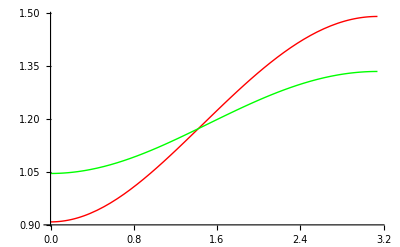

```mathematica
p1 = Plot[θ[φ]/.{L1->1,L2->.75,L3->.2,L4->1},{φ,0,Pi},PlotStyle->RGBColor[1,0,0]];
p2= Plot[θ[φ]/.{L1->1,L2->.75,L3->.1,L4->1},{φ,0,Pi},PlotStyle->RGBColor[0,1,0]];
Show[p1,p2,DisplayFunction->$DisplayFunction]
```

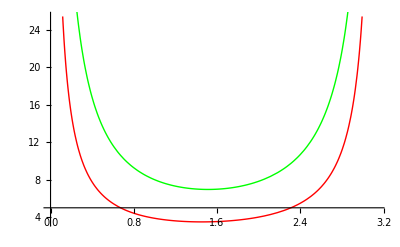

```mathematica
p1=Plot[KT[φ]/.{L1->1,L2->.75,L3->.2,L4->1},{φ,0,Pi},PlotStyle->RGBColor[1,0,0]];
p2=Plot[KT[φ]/.{L1->1,L2->.75,L3->.1,L4->1},{φ,0,Pi},PlotStyle->RGBColor[0,1,0]];
Show[p1,p2,DisplayFunction->$DisplayFunction]
```

## Heuristic model

```mathematica
ClearMech[];ClearAll["Global`*"]; Needs["MechanicalSystems`Modeler2D`"];Off[General::"spell"];Off[General::"spelll"];
```

ClearAll::wrsym: Symbol T is Protected.

```mathematica
pVals = {m->.003,k->15,hIn->.02,hOut ->.04,θInitial->Pi};
```

```mathematica
θ[t_]=θ[t]/.DSolve[{k hIn^2 θ[t]+hOut^2 m  θ''[t]==0,θ'[0]==0,θ[0]==θInitial},θ[t],t][[1]]
```

θInitial Cos[(hIn √k t)/(hOut √m)]

```mathematica
θ'[t]
```

-(hIn √k θInitial Sin[(hIn √k t)/(hOut √m)])/(hOut √m)

```mathematica
FullSimplify[θ''[t]]
```

-(hIn^2 k θInitial Cos[(hIn √k t)/(hOut √m)])/(hOut^2 m)

```mathematica
FullSimplify[m θ'[t]]
```

-(hIn √k √m θInitial Sin[(hIn √k t)/(hOut √m)])/hOut

```mathematica
θ[t]/.pVals/.{t->1}
```

-2.19368

```mathematica
period=2 * Pi/((hIn √k)/(hOut √m))/.pVals
```

0.177715

```mathematica
Plot[θ[t]/.pVals,{t,0,.05}]
```

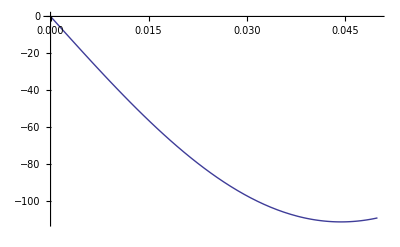

```mathematica
Plot[θ'[t]/.pVals,{t,0,.05}]
```

## Heuristic model 2

```mathematica
ClearMech[];ClearAll["Global`*"]; Needs["MechanicalSystems`Modeler2D`"];Off[General::"spell"];Off[General::"spelll"];
```

ClearAll::wrsym: Symbol T is Protected.

```mathematica
pVals = {m->.003,k->15,hIn->.02,hOut ->.04,θInitial->Pi,B->1};
```

```mathematica
θ[t_]=θ[t]/.DSolve[{k( hIn-B θ[t])^2 θ[t]+hOut^2 m  θ''[t]==0,θ'[0]==0,θ[0]==θInitial},θ[t],t][[1]];
```

DSolve::bvimp: General solution contains implicit solutions. In the boundary value problem these solutions will be ignored, so some of the solutions will be lost.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

ReplaceAll::reps: {{} ⟦ 1 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: "reps" will be suppressed during this calculation.

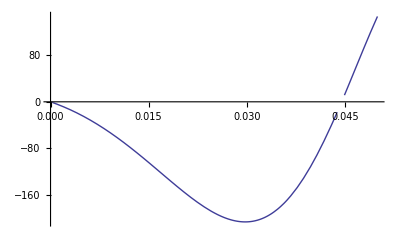

```mathematica
Plot[θ'[t]/.pVals,{t,0,.05}]
```

## Heuristic model with linear change in in-lever

```mathematica
ClearMech[];ClearAll["Global`*"]; Needs["MechanicalSystems`Modeler2D`"];Off[General::"spell"];Off[General::"spelll"];
```

ClearAll::wrsym: Symbol T is Protected.

```mathematica
numLs = 5;
pVals = {m->1,k->1,hIn->.5,hOut ->1,θInitial->Pi,B->.1};
tSim = 10;
```

```mathematica
θN[t_]=θ[t]/.NDSolve[{k( hIn-B t)^2 θ[t]+hOut^2 m  θ''[t]==0,θ'[0]==0,θ[0]==θInitial}
/.pVals,θ,{t,0,tSim}][[1]];
```

```mathematica
θ[t_]=θ[t]/.DSolve[{k hIn^2 θ[t]+hOut^2 m  θ''[t]==0,θ'[0]==0,θ[0]==θInitial},θ[t],t][[1]];
```

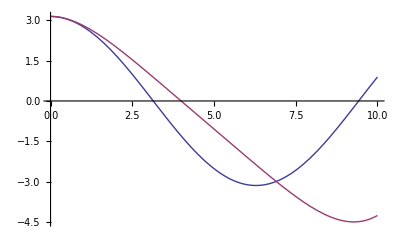

```mathematica
Plot[{θ[t]/.pVals,θN[t]},{t,0,tSim}]
```

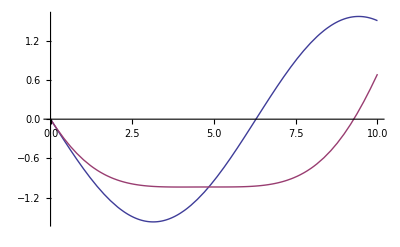

```mathematica
Plot[{θ'[t]/.pVals,θN'[t]},{t,0,tSim}]
```

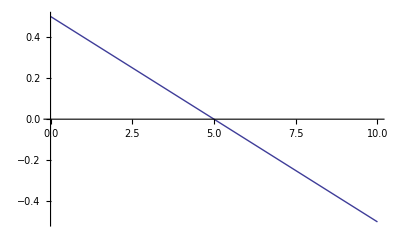

```mathematica
Plot[ (hIn-B t)/.pVals,{t,0,tSim}]
```

## Heuristic model with linear change in out-lever

```mathematica
ClearMech[];ClearAll["Global`*"]; Needs["MechanicalSystems`Modeler2D`"];Off[General::"spell"];Off[General::"spelll"];
```

ClearAll::wrsym: Symbol T is Protected.

```mathematica
numLs = 5;
pVals = {m->1,k->1,hIn->.5,hOut ->1,θInitial->Pi,B->1*.1};
tSim = 10;
```

```mathematica
θN[t_]=θ[t]/.NDSolve[{k hIn^2 θ[t]+(hOut+B t)^2 m  θ''[t]==0,θ'[0]==0,θ[0]==θInitial}
/.pVals,θ,{t,0,tSim}][[1]];
```

```mathematica
θ[t_]=θ[t]/.DSolve[{k hIn^2 θ[t]+(hOut+B t)^2 m  θ''[t]==0,θ'[0]==0,θ[0]==θInitial},θ[t],t][[1]];
```

```mathematica
v[t_]=θ'[t] (hOut+B t);
```

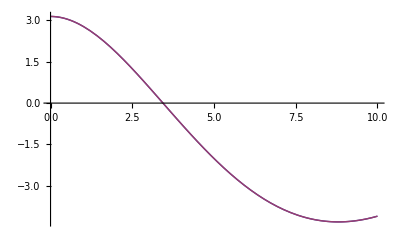

```mathematica
Plot[{θ[t]/.pVals,θN[t]},{t,0,tSim}]
```

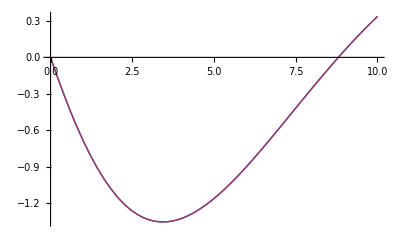

```mathematica
Plot[{θ'[t]/.pVals,θN'[t]},{t,0,tSim}]
```

```mathematica
FullSimplify[θ'[t]]
```

-(hIn √k θInitial Sin[(hIn √k t)/(hOut √m)])/(hOut √m)

```mathematica
N[(θ'[t] )/.pVals/.{t->3.14}]
```

-1.5708

-1.34632-2.77556×10^-17 ⅈ

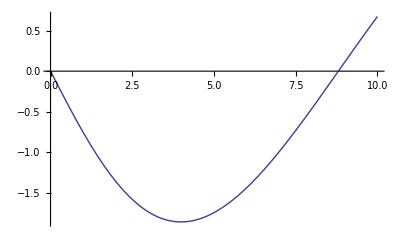

```mathematica
Plot[v[t]/.pVals,{t,0,tSim}]
```

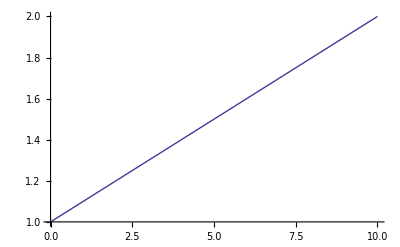

```mathematica
Plot[ (hOut+B t)/.pVals,{t,0,tSim}]
```

## Heuristic model with nonlinear in-lever (unfinished)

```mathematica
ClearMech[];ClearAll["Global`*"]; Needs["MechanicalSystems`Modeler2D`"];Off[General::"spell"];Off[General::"spelll"];
```

ClearAll::wrsym: Symbol T is Protected.

```mathematica
numLs = 5;
pVals = {m->.003,k->15,hOut->.04,θInitial->Pi};
lVals = {L1->1,L2->.75,L4->1};
```

```mathematica
KT[φ_]:=(L1 L2 √(1-((L1^2+L2^2-L3^2-L4^2+2 L3 L4 Cos[φ])^2)/(4 L1^2 L2^2)) Csc[φ])/(L3 L4)
```

```mathematica
KTval[θ_]=KT[ .9θ+Pi/50]/.lVals;
```

```mathematica
L3vals = Range[.2*.5,.2*1.5,.2 (1.5-0.5)/numLs];
dataList={};
```

```mathematica
For [i=1,i<numLs+1,
	L3=L3vals[[i]];
θ[t_]=θ[t]/.NDSolve[{k (hOut/KTval[θ[t]])^2 θ[t]+hOut^2 m  θ''[t]==0,θ'[0]==0,θ[0]==θInitial}
/.pVals,θ,{t,0,2}][[1]];
dataList=Append[dataList,{Log[KT[Pi/2]/.lVals,10],Log[Max[θ'[t]/.{t->Table[t,{t,0,2,2/1000}]}],10]}];
Clear[θ];
i++]
```

```mathematica
line=Fit[dataList,{1,x},x]
```

0.871262-0.143722 x

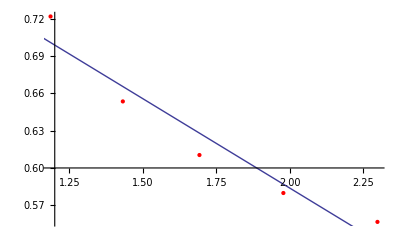

```mathematica
Show[ListPlot[dataList,PlotStyle->Red],Plot[line,{x,1.,2.4}]]
```

## Gear model

```mathematica
ClearMech[];ClearAll["Global`*"]; Needs["MechanicalSystems`Modeler2D`"];Off[General::"spell"];Off[General::"spelll"];
```

ClearAll::wrsym: Symbol T is Protected.

```mathematica
numLs = 5;
pVals = {m->1,k->1,hIn->.5,hOut ->1,θ0->Pi/4,B->1*.1};
tSim = 10;
```

```mathematica
θ[t_]=θ[t]/.FullSimplify[DSolve[{m hOut^2  gr^2 θ''[t]+k θ[t]-k θR==0,θ'[0]==0,θ[0]==θ0},θ[t],t]][[1]]
```

θR+(θ0-θR) Cos[(√k t)/(gr hOut √m)]

```mathematica
θ'[t]
```

-(√k (θ0-θR) Sin[(√k t)/(gr hOut √m)])/(gr hOut √m)

```mathematica
v= θ'[t] gr hOut
```

-(√k (θ0-θR) Sin[(√k t)/(gr hOut √m)])/(√m)

## Gear model with drag - no solution

```mathematica
ClearMech[];ClearAll["Global`*"]; Needs["MechanicalSystems`Modeler2D`"];Off[General::"spell"];Off[General::"spelll"];
```

ClearAll::wrsym: Symbol T is Protected.

```mathematica
numLs = 5;
pVals = {m->1,k->1,hIn->.5,hOut ->1,θ0->Pi/4,B->1*.1};
tSim = 10;
```

```mathematica
θ[t_]=θ[t]/.FullSimplify[DSolve[{m hOut^2  gr^2 θ''[t]+Cd (θ'[t])^2 +k θ[t]-k θR==0,θ'[0]==0,θ[0]==θ0},θ[t],t]][[1]]
```

ReplaceAll::reps: k θR == k θ[t] + Cd SuperscriptBox[SuperscriptBox[θ0 == θ[0] is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

ReplaceAll::reps: {k\ θR == Cd\ (∂_t (Hold[« 1 »]/. Hold[« 1 »]))^2 + gr^2\ « 3 » + k\ (Hold[θ[« 1 »]]/. Hold[{« 3 »}]/. {Times[« 2 »] == Plus[« 2 »], D[« 2 »] == 0, θ0 == ReplaceAll[« 2 »]}), « 1 », θ0 == « 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

ReplaceAll::reps: {k\ θR == Cd\ (∂_t (Hold[« 1 »]/. Hold[« 1 »]))^2 + gr^2\ « 3 » + k\ (Hold[θ[« 1 »]]/. Hold[{« 3 »}]/. {Times[« 2 »] == Plus[« 2 »], D[« 2 »] == 0, θ0 == ReplaceAll[« 2 »]}), « 1 », θ0 == « 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

ReplaceAll::reps: {k\ θR == Cd\ (∂_t (Hold[« 1 »]/. Hold[« 1 »]))^2 + gr^2\ « 3 » + k\ (Hold[θ[« 1 »]]/. Hold[{« 3 »}]/. {Times[« 2 »] == Plus[« 2 »], D[« 2 »] == 0, θ0 == ReplaceAll[« 2 »]}), « 1 », θ0 == « 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

ReplaceAll::reps: {k\ θR == Cd\ (∂_t (Hold[« 1 »]/. Hold[« 1 »]))^2 + gr^2\ « 3 » + k\ (Hold[θ[« 1 »]]/. Hold[{« 3 »}]/. {Times[« 2 »] == Plus[« 2 »], D[« 2 »] == 0, θ0 == ReplaceAll[« 2 »]}), « 1 », θ0 == « 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

$Aborted

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

$Aborted

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

General::ivar: 0 is not a valid variable.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

$Aborted

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

ReplaceAll::reps: {k\ θR == Cd\ (∂_0 (Hold[« 1 »]/. Hold[« 1 »]))^2 + gr^2\ « 3 » + k\ (Hold[θ[« 1 »]]/. Hold[{« 3 »}]/. {Times[« 2 »] == Plus[« 3 »], D[« 2 »] == 0, θ0 == ReplaceAll[« 2 »]}), « 1 », θ0 == « 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {k\ θR == Cd\ (∂_t (ReplaceAll[« 2 »]/. {« 3 »}))^2 + « 1 » + k\ (Hold[« 1 »]/. Hold[« 1 »]/. {Equal[« 2 »], Equal[« 2 »], Equal[« 2 »]}/. {« 1 »}), « 1 », θ0 == (« 1 »/. {« 1 »})} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$Aborted

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$Aborted

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$Aborted

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

ReplaceAll::reps: « 1 » is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: Hold[{k θR == k θ[t] + Cd SuperscriptBox[« 1 », TagBox[(« 1 »), Derivative], Rule[MultilineFunction, None]][« 1 »]^2 + gr^2 hOut^2 m SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

$Aborted

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

ReplaceAll::reps: Hold[{k θR == k θ[t] + Cd SuperscriptBox[« 1 », TagBox[(« 1 »), Derivative], Rule[MultilineFunction, None]][« 1 »]^2 + gr^2 hOut^2 m SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$Aborted

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

ReplaceAll::reps: k θR == k (Hold[θ[t]]/. Hold[{Times[« 2 »] == Plus[« 3 »], SuperscriptBox[« 1 », TagBox[(« 1 »), Derivative], Rule[MultilineFunction, None]][« 1 »] == 0, θ0 == θ[« 1 »]}])« 1 » « 1 » == 0θ0 == (Hold[θ[0]]/. Hold[{k θR == « 1 », SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

ReplaceAll::reps: Hold[{k θR == k θ[t] + Cd SuperscriptBox[« 1 », TagBox[(« 1 »), Derivative], Rule[MultilineFunction, None]][« 1 »]^2 + gr^2 hOut^2 m SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

$Aborted

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

ReplaceAll::reps: Hold[{k θR == k θ[t] + Cd SuperscriptBox[« 1 », TagBox[(« 1 »), Derivative], Rule[MultilineFunction, None]][« 1 »]^2 + gr^2 hOut^2 m SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

$Aborted

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

ReplaceAll::reps: Hold[{k θR == k θ[t] + Cd SuperscriptBox[« 1 », TagBox[(« 1 »), Derivative], Rule[MultilineFunction, None]][« 1 »]^2 + gr^2 hOut^2 m SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

ReplaceAll::reps: Hold[{k θR == k θ[t] + Cd SuperscriptBox[« 1 », TagBox[(« 1 »), Derivative], Rule[MultilineFunction, None]][« 1 »]^2 + gr^2 hOut^2 m SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

ReplaceAll::reps: k θR == k (Hold[θ[t]]/. Hold[{Times[« 2 »] == Plus[« 3 »], SuperscriptBox[« 1 », TagBox[(« 1 »), Derivative], Rule[MultilineFunction, None]][« 1 »] == 0, θ0 == θ[« 1 »]}])« 1 » « 1 » == 0θ0 == (Hold[θ[0]]/. Hold[{k θR == « 1 », SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

ReplaceAll::reps: {k\ θR == Cd\ (∂_t (Hold[« 1 »]/. Hold[« 1 »]))^2 + « 1 » + k\ (Hold[θ[« 1 »]]/. Hold[{« 3 »}]/. {Times[« 2 »] == Times[« 2 »], D[« 2 »] == 0, θ0 == ReplaceAll[« 2 »]}), « 1 », θ0 == (« 1 »)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

ReplaceAll::reps: « 1 » is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: Hold[{k θR == k θ[t] + Cd SuperscriptBox[« 1 », TagBox[(« 1 »), Derivative], Rule[MultilineFunction, None]][« 1 »]^2 + gr^2 hOut^2 m SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

ReplaceAll::reps: Hold[{k θR == k θ[t] + Cd SuperscriptBox[« 1 », TagBox[(« 1 »), Derivative], Rule[MultilineFunction, None]][« 1 »]^2 + gr^2 hOut^2 m SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

ReplaceAll::reps: k θR == k (Hold[θ[t]]/. Hold[{Times[« 2 »] == Plus[« 3 »], SuperscriptBox[« 1 », TagBox[(« 1 »), Derivative], Rule[MultilineFunction, None]][« 1 »] == 0, θ0 == θ[« 1 »]}])« 1 » « 1 » == 0θ0 == (Hold[θ[0]]/. Hold[{k θR == « 1 », SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

ReplaceAll::reps: Hold[{k θR == k θ[t] + Cd SuperscriptBox[« 1 », TagBox[(« 1 »), Derivative], Rule[MultilineFunction, None]][« 1 »]^2 + gr^2 hOut^2 m SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

ReplaceAll::reps: Hold[{k θR == k θ[t] + Cd SuperscriptBox[« 1 », TagBox[(« 1 »), Derivative], Rule[MultilineFunction, None]][« 1 »]^2 + gr^2 hOut^2 m SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

ReplaceAll::reps: Hold[{k θR == k θ[t] + Cd SuperscriptBox[« 1 », TagBox[(« 1 »), Derivative], Rule[MultilineFunction, None]][« 1 »]^2 + gr^2 hOut^2 m SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

ReplaceAll::reps: Hold[{k θR == k θ[t] + Cd SuperscriptBox[« 1 », TagBox[(« 1 »), Derivative], Rule[MultilineFunction, None]][« 1 »]^2 + gr^2 hOut^2 m SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

ReplaceAll::reps: k θR == k (Hold[θ[t]]/. Hold[{Times[« 2 »] == Plus[« 3 »], SuperscriptBox[« 1 », TagBox[(« 1 »), Derivative], Rule[MultilineFunction, None]][« 1 »] == 0, θ0 == θ[« 1 »]}])« 1 » « 1 » == 0θ0 == (Hold[θ[0]]/. Hold[{k θR == « 1 », SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

ReplaceAll::reps: {k\ θR == Cd\ (∂_t (Hold[« 1 »]/. Hold[« 1 »]))^2 + « 1 » + k\ (Hold[θ[« 1 »]]/. Hold[{« 3 »}]/. {Times[« 2 »] == Times[« 2 »], D[« 2 »] == 0, θ0 == ReplaceAll[« 2 »]}), « 1 », θ0 == (« 1 »)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

General::ivar: 0 is not a valid variable.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

ReplaceAll::reps: {k\ θR == Cd\ (∂_0 (Hold[« 1 »]/. Hold[« 1 »]))^2 + gr^2\ « 3 » + k\ (Hold[θ[« 1 »]]/. Hold[{« 3 »}]/. {Times[« 2 »] == Plus[« 3 »], D[« 2 »] == 0, θ0 == ReplaceAll[« 2 »]}), « 1 », θ0 == « 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {k\ θR == Cd\ (∂_t (ReplaceAll[« 2 »]/. {« 3 »}))^2 + « 1 » + k\ (Hold[« 1 »]/. Hold[« 1 »]/. {Equal[« 2 »], Equal[« 2 »], Equal[« 2 »]}/. {« 1 »}), « 1 », θ0 == (« 1 »/. {« 1 »})} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: "reclim" will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

```mathematica
θ'[t]
```

-(√k (θ0-θR) Sin[(√k t)/(gr hOut √m)])/(gr hOut √m)

```mathematica
v= θ'[t] gr hOut
```

-(√k (θ0-θR) Sin[(√k t)/(gr hOut √m)])/(√m)

## Import parameter values (instead of defining)

### Set parameters

```mathematica
KillMech[];ClearMech[];ClearAll["Global`*"]; Needs["MechanicalSystems`Modeler2D`"];Off[General::"spell"];
```

ClearMech::shdw: Symbol "ClearMech" appears in multiple contexts {"MechanicalSystems`Modeler2D`", "Global`"}; definitions in context "MechanicalSystems`Modeler2D`" may shadow or be shadowed by other definitions.

```mathematica
currPath = Import["/Volumes/Docs/Projects/Patek_project/pod_model/sims/curr_path.txt",{"Text","Lines"}];
```

```mathematica
currPath
```

{/Volumes/Docs/Projects/Patek_project/pod_model/sims/s001}

```mathematica
inParams = Import[StringJoin[currPath, "/input_params.mat"]][[1]];
```

```mathematica
tEvalIn = Import[StringJoin[currPath, "/eval_time.mat"]][[1]];
```

```mathematica
L1In = inParams[[1]];
L2In=inParams[[2]];
L3In=inParams[[3]];
L4In=inParams[[4]];

EXLocalIn = inParams[[5]];
EYLocalIn=inParams[[6]];
FXLocalIn=inParams[[7]];
FYLocalIn=inParams[[8]];

thetaStartIn=inParams[[9]];
dMassIn=inParams[[10]];
dIIn=inParams[[11]];
kSpringIn=inParams[[12]];
thetaRestIn=inParams[[13]];

simDurationIn=inParams[[14]];
dAIn=inParams[[15]];
rhoIn=inParams[[16]];
CdIn=inParams[[17]];
waterIIn = inParams[[18]];
mxErrIn = inParams[[19]];
```

```mathematica
Clear[inParams]
```

## Define parameter values (instead of importing)

```mathematica
ClearMech[];ClearAll["Global`*"]; Needs["MechanicalSystems`Modeler2D`"];Off[General::"spell"];Off[General::"spelll"];
```

ClearAll::wrsym: Symbol T is Protected.

```mathematica
(* Linakage coordinates *)
L1In=6 *10^-3;
L2In=3.75 *10^-3;
L3In=.425*10^-3;
L4In=6.7 *10^-3;
L5In=6.1* 10^-3;
dacLenIn = 9.63*10^-3;
```

```mathematica
(* Distance between points A&F,determined by propodus thickness *)
hAFIn = 1 10^-3;
```

```mathematica
(* Initial input angle (rad) *)
thetaStartIn = 1.3774;
```

```mathematica
(* Dactyl mass (kg) *)
dMassIn = 4.53 *10^-4 ;
```

```mathematica
(* Dactyl I (kg m^2) *)
dIIn= 8.16 *10^-8 ;
```

```mathematica
(* Water I (kg m^2) *)
waterIIn = 1*10^-8;
```

```mathematica
(* 3rd moment of area of dactyl *)
dAIn=1.5 * 10^-11;
```

```mathematica
(* Drag coefficient of elliptical dactyl element *)
DIn = 0.07;
```

```mathematica
(* Torsion spring at mV joint (Nm/rad) *)
kSpringIn = (60*10^3) (3.18 *10^-3)^2;
```

```mathematica
(* Resting position for torsion spring *)
thetaRestIn = 1.6088;

gammaIn = 60*Pi/180;
```

```mathematica
(* Density of water (kg/m^3) *)
rhoIn=998;
```

```mathematica
(* Duration of simulation (s) *)
simDurationIn = 6*10^-3;
```

```mathematica
(* Time values to evaluate results *)
tEvalIn = Table[N[i],{i,0,simDurationIn,simDurationIn/1000}];
```

```mathematica
(* Precision of simulation *)
mxErrIn = 10^-5;
```

```mathematica
(* Designate current path *)
currPath="/Volumes/Docs/Projects/Patek_project/sims";
```

## Phenomeological model

### Rescale input parameter values

Scale Factors (Mutliplers of all parameters -- helps with numerical instabilities)

```mathematica
sL = 1 / L1In;
sM = 1/dMassIn;
sT=10^3;
```

```mathematica
(* Apply scale factors to parameters *)
dMass = dMassIn sM;
dI= dIIn sM sL^2;
waterI=waterIIn sM sL^2;

L1=L1In sL;
L2=L2In sL;
L3=L3In sL;
L4=L4In  sL;
L5=L5In sL;
dacLen = dacLenIn sL;

(*EXLocal = EXLocalIn sL;
EYLocal = EYLocalIn sL;
FXLocal = FXLocalIn sL;
FYLocal = FYLocalIn sL;*)
hAF = hAFIn sL;
thetaStart    = thetaStartIn;
gamma = gammaIn;

kSpring = kSpringIn (sM sL^2/sT^2);
thetaRest= thetaRestIn;
dA = dAIn * sL^5;
rho = rhoIn * sM / sL^3;
DrgIdx =0* DIn;

simDuration = simDurationIn * sT;
tEval = tEvalIn*sT;

mxErr = mxErrIn;
```

```mathematica
Clear[dMassIn, dIIn,L1In,L2In,L3In,L4In,L5In,kSpringIn,TmaxIn,hAFIn,thetaIn,simDurationIn,tEvalIn,simDurationIn,tEvalIn,dAIn,rhoIn,CdIn,waterIIn,mxErrIn,LCOMIn]
```

### Calculated parameter values, define model inputs

Angle, ψ, btwn L1 & L4:

```mathematica
(* Distance btwn B & D *)
hBD=√(L1^2+L2^2-2 L1 L2 Cos[thetaStart]);

(* This angle btwn 1 & 4 *)
si=ArcCos[(hBD^2+L1^2-L2^2)/(2 hBD L1)]+ArcCos[(hBD^2+L4^2-L3^2)/(2 hBD L4)];

(* Distance btwn B & F: *)
hBF=√(hAF^2+L2^2+2 hAF L2 Cos[thetaStart]);
```

```mathematica
ArcCos[(hBD^2+L4^2-L3^2)/(2 hBD L4)]
```

0.0506499

Check that the geometry is possible (both should be 'True')

```mathematica
L4  < ( L3 + hBD)
```

True

```mathematica
L4  > (  hBD-L3)
```

True

```mathematica
L4/sL
```

0.0067

```mathematica
L1^2+L2^2-2 L1 L2 Cos[thetaStart]
```

1.15038

```mathematica
L1
```

1

```mathematica
si
```

0.659415

Points on the appendage

```mathematica
AX=0;
AY= 0;
BX=L2 Sin[thetaStart];
BY=L2 Cos[thetaStart];
CX=L4 Sin[si];
CY=L1-L4 Cos[si];
DX=0;
DY=L1;
FX = 0;
FY=-hAF;
GX=FX-L5 Sin[gamma];
GY=FY+L5 Cos[gamma];

(*EX =BX+ EXLocal;
EY=BY - EYLocal;
FX=BX- FXLocal;
FY=EY-FYLocal;*)
```

```mathematica
Clear[si,hAF,hBF]
```

```mathematica
(* Check distances *)
Sqrt[(BX-CX)^2+(BY-CY)^2]
L3
```

0.0708333

0.0708333

```mathematica
si
```

si

Body addresses

```mathematica
ground = 1; mV = 2;carpus = 3;dactyl = 4;
```

Display initial geometry

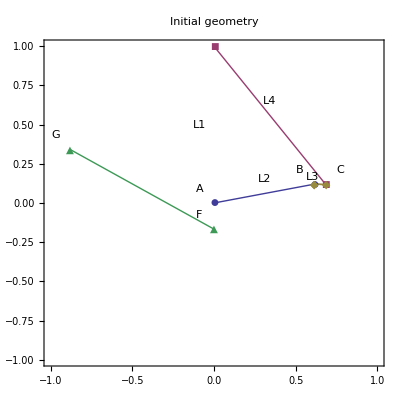

```mathematica
offset = .09 L1;
Show[
ListPlot[{
{{AX,AY},{BX,BY}},
{{CX,CY},{DX,DY}},
{{BX,BY},{CX,CY},{BX,BY}},
{{GX,GY},{FX,FY}}
},
PlotMarkers->Automatic,Joined->True,
Frame->True,AspectRatio->Automatic,
PlotLabel->"Initial geometry",
PlotRange->{{-1,1},{-1,1}}],
Graphics[
{Text["A",{AX-offset,AY+offset}],Text["B",{BX-offset,BY+offset}],
Text["C",{CX+offset,CY+offset}],Text["D",{DX-offset,DY+offset}],
Text["F",{FX-offset,FY+offset}],
Text["G",{GX-offset,GY+offset}],
Text["L1",{Mean[{AX,DX}]-offset,Mean[{AY,DY}]}],
Text["L2",{Mean[{AX,BX}]-offset,Mean[{AY,BY}]}+offset],
Text["L3",{Mean[{CX,BX}]-offset,Mean[{CY,BY}]}+offset/2],
Text["L4",{Mean[{DX,CX}]-offset,Mean[{DY,CY}]}+offset]
}]
]
```

### Define Bodies

```mathematica
bd[ground] = Body[ground,
PointList->{
(*P1*){DX,DY}},
InitialGuess->{
{0,0},0}
];
```

```mathematica
bd[mV] = Body[mV,
PointList->{
(*P1*){BX,BY}},
Centroid->{0,0},
InitialGuess->{
{0,0},0}
];
```

```mathematica
bd[carpus]=Body[carpus,
PointList->{(*P1*){CX-BX,CY-BY},
                       (*P2*){FX-BX,FY-BY},
                       (*P3*){GX-BX,GY-BY}},
Mass->dMass,Inertia->dI+waterI,
InitialGuess->{{BX,BY},0}];
```

bd[dactyl] = Body[dactyl, PointList -> {(*P1*){GX - FX, GY - FY}}, Mass -> dMass, Inertia -> dI + waterI, InitialGuess -> {{FX, FY}, 0}];

```mathematica
SetBodies[bd[ground],bd[mV],bd[carpus]];
```

### Define constraints

Pin joint between ground and mV:

```mathematica
cs[1]= Revolute2[1,Point[ground,0],Point[mV,0]];
```

Initially fix position of joint at mV origin (removed later):

```mathematica
cs[2] = RotationLock1[2,  mV,0];
```

Pin joint between carpus and mV:

```mathematica
cs[3] = Revolute2[3, Point[carpus, 0], Point[mV, 1]];
```

Fix distance between ground and top of carpus:

```mathematica
cs[4] = RelativeDistance1[4, Point[carpus, 1], Point[ground, 1], L4];
```

Pin btwn carpus and dactyl

cs[5] = Revolute2[5, Point[dactyl, 0], Point[carpus, 2]];

Lock rotation btwn carpus & dactyl

cs[6] = RotationLock1[6, carpus, dactyl, 0];

```mathematica
SetConstraints[cs[1], cs[2], cs[3], cs[4]];
```

```mathematica
Print["Check system after constraints:" Evaluate[CheckSystem[]]]
```

Check system after constraints: True

### Evaluate kinematic model

SetParameters[{
   (*Torsion spring stiffness*)  theta -> θ
   }];

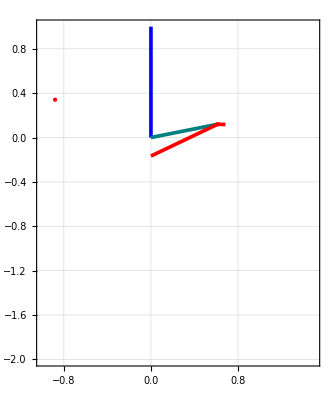

```mathematica
graph=Graphics[{
(*ground*){RGBColor[0,0,1],Bar[Axis[ground,0,1],10^-4 sL,10^-4 sL]},
(*mV*){RGBColor[0,.5,.5],Bar[Line[mV,0,1],10^-4 sL,10^-4 sL]},
(*carpus1*){RGBColor[1,0,0],Bar[Line[carpus,0,1],10^-4 sL,10^-4 sL]},
(*carpus2*){RGBColor[1,0,0],Bar[Line[carpus,0,2],10^-4 sL,10^-4 sL]},
(*carpus3*){RGBColor[1,0,0],Vertex[carpus,{0,3}]}
},
Frame->True,
AspectRatio->Automatic,
GridLines->Automatic,
PlotRange->{{-1,1.5},{-2,1}}
];

Show[graph/.SolveMech[]]
```

```mathematica
Evaluate[{Angle[mV,1]}/.SolveMech[]] (180/π)
```

{11.0808}

### Define Loads

Moment created by the spring

springMoment = kSpring  ( Pi/2 - Angle[mV, 1] - thetaRest);

```mathematica
springMoment=kSpring (Pi/2-Angle[mV,1]-thetaRest);
dragMoment=(-0.5*rho*(Velocity[carpus][[3]])^2*(dacLen^5)*DrgIdx) (Velocity[carpus][[3]]/Abs[10^-20+Velocity[carpus][[3]]]);
```

```mathematica
ld[1]=Moment[mV,springMoment];
```

Drag on dactyl

ld[2] = Force[dactyl, Axis[Point[dactyl, 1], -Velocity[dactyl, 1]^2], 5.0, Magnitude -> Relative];

```mathematica
ld[2]=Moment[carpus,dragMoment];
```

```mathematica
ld[3]=Gravity[{0,-1},0];
```

```mathematica
SetLoads[ld[1],ld[2]]
```

```mathematica
Print["Check system after loads:" Evaluate[CheckSystem[]]]
```

Check system after loads: True

### Find solution

Solution with the 4-bar linkage constrained from moving:

Remove constraint 2 (fixed angle of the mV)  & define initial conditions

```mathematica
fsys = SetFree[2,{Solution->Dynamic,
InitialCondition->{T->0,Θ2d->0,Θ3d->0,Θ4d->0,X2d->0,Y2d->0,X3d->0,Y3d->0,X4d->0,Y4d->0}}];
```

SolveFree[fsys]

```mathematica
(* Default solver *)
sol = SolveFree[fsys, simDuration, MakeRules -> {Location, Velocity, Acceleration},
MaxError->mxErr];
```

(* High precision solver *)
sol = SolveFree[fsys, simDuration, MakeRules -> {Location, Velocity, Acceleration},
   ConstraintCorrection -> True,
   MaxError -> 10^-7,
   Method -> Corrector,
   FitDegree -> Quadratic,
   MaxSteps -> 5000];

### Simulation diagnostics (for debugging)

```mathematica
Constraints[1]/.sol
Constraints[3]/.sol
Constraints[4]/.sol
```

{0,0}

{-0.613348 Cos[InterpolatingFunction[{{0.,6.}},<>][T]]+0.120121 Sin[InterpolatingFunction[{{0.,6.}},<>][T]]+InterpolatingFunction[{{0.,6.}},<>][T],-0.120121 Cos[InterpolatingFunction[{{0.,6.}},<>][T]]-0.613348 Sin[InterpolatingFunction[{{0.,6.}},<>][T]]+InterpolatingFunction[{{0.,6.}},<>][T]}

{-1.24694+(-1-0.00267907 Cos[InterpolatingFunction[{{0.,6.}},<>][T]]+0.0707827 Sin[InterpolatingFunction[{{0.,6.}},<>][T]]+InterpolatingFunction[{{0.,6.}},<>][T])^2+(0.0707827 Cos[InterpolatingFunction[{{0.,6.}},<>][T]]+0.00267907 Sin[InterpolatingFunction[{{0.,6.}},<>][T]]+InterpolatingFunction[{{0.,6.}},<>][T])^2}

```mathematica
StepMech[]
```

{X2→0.,Y2→0.,Θ2→0.,X3→0.613348,Y3→0.120121,Θ3→0.}

```mathematica
Loads[dactyl,Coordinates->Global][[2]]
```

Mech::nobody: Body number 4 is not present in the current system.

Loads::argmbmso: Loads called with invalid arguments. Loads[bnum, options] or
Loads[symbol, options] is expected. Body numbers are specified by positive integers.

Coordinates→Global

```mathematica
(Loads[carpus,Coordinates->Global])/.sol/.{T->tEval}
```

{{0,0},0}

### Draw bodies

```mathematica
graph = Graphics[{
{RGBColor[0, 0, 1], Bar[Line[ground, 0, 1], sL/10^4, sL/10^4]}, 
{RGBColor[0, 0.5, 0.5], Bar[Line[mV, 0, 1], sL/10^4, sL/10^4]}, 
(*carpus1*){RGBColor[1,0,0],Bar[Line[carpus,0,1],10^-4 sL,10^-4 sL]},
(*carpus2*){RGBColor[1,0,0],Bar[Line[carpus,0,2],10^-4 sL,10^-4 sL]},
(*carpus3*){RGBColor[1,0,0],Vertex[carpus,{0,3}]}}, 
Frame -> True, AspectRatio -> Automatic, GridLines -> Automatic];
```

```mathematica
EY
```

EY

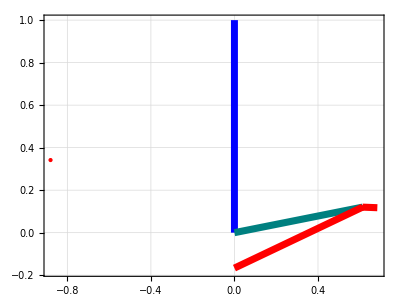

```mathematica
Show[graph/.(sol/.{T->0*simDuration})]
```

numPlot = 10; GraphicsGrid[{graph /. (sol /. Table[{T -> i}, {i, 0, simDuration, simDuration/numPlot}] )}]

```mathematica
Animate[Show[graph /. (sol /. {T -> i})], {i, 0, simDuration, .1}]
```

### Graph results

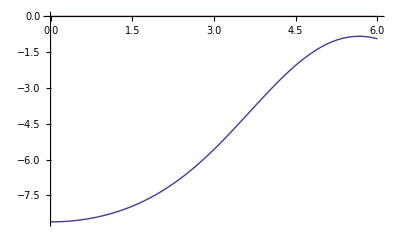

```mathematica
Plot[{(springMoment/.sol),T*0},{T,0,simDuration}]
```

```mathematica
(180/Pi) Tmax/kSpring
```

1.53999 Tmax

```mathematica
180/Pi thetaRest
```

92.1775

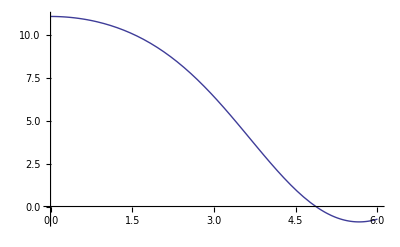

```mathematica
Plot[(180/Pi)(Angle[mV,1])/.sol,{T,0,simDuration}]
```

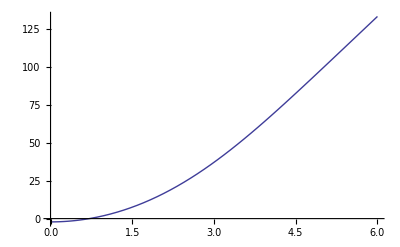

```mathematica
Plot[(180/Pi)(Angle[carpus,1])/.sol,{T,0,simDuration}]
```

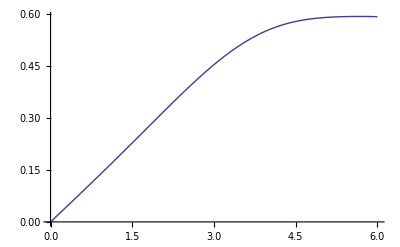

```mathematica
Plot[Velocity[carpus][[3]]/.sol,{T,0,simDuration}]
```

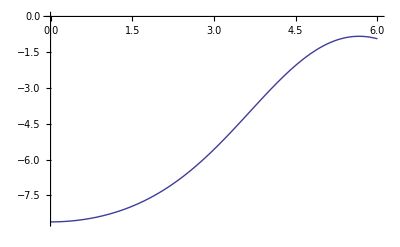

```mathematica
Plot[springMoment/.sol,{T,0,simDuration}]
```

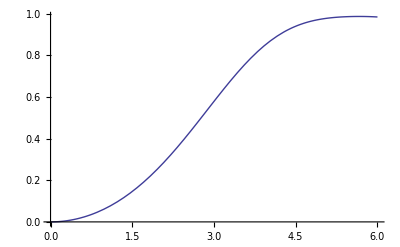

```mathematica
Plot[BodyEnergy[carpus]/.sol,{T,0,simDuration}]
```

### Energetics

springEnergy[T_] := -((Angle[mV, 1] - thetaRest)/Abs[(Angle[mV, 1] - thetaRest)]) 0.5 kSpring (Angle[mV, 1] - thetaRest)^2 ;

```mathematica
springEnergy=Abs[0.5springMoment(Pi/2-Angle[mV,1]-thetaRest)/.sol];
```

```mathematica
dacSpeed=Sqrt[
(Velocity[carpus,3][[1]])^2+(Velocity[carpus,3][[2]])^2]/.sol;
```

dragEnergy[ti_] := NIntegrate[totDrag[t], {t, 0, ti}];

kineEnergy =(*Rotation *)(0.5 (dI + waterI) Velocity[carpus][[3]]^2  +
             (* Translation *) 0.5 dMass dacSpeed^2) /. sol;

```mathematica
kineEnergy=(*Rotation *)(0.5 (dI+waterI) Velocity[carpus][[3]]^2 ) /.sol;
```

```mathematica
kineEnergyMat = BodyEnergy[carpus]/.sol;
```

```mathematica
kineEnergy/.{T->2}
```

0.263696

```mathematica
totEnergy = springEnergy  + kineEnergy;
```

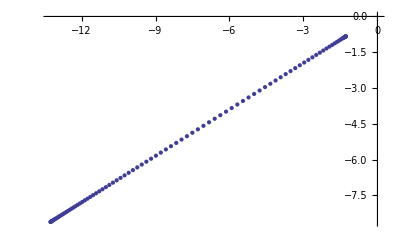

```mathematica
ListPlot[Table[{((180/Pi) (Pi/2-Angle[mV,1] -thetaRest)) /. sol, springMoment /. sol}, {T, simDuration/100, simDuration - simDuration/100, simDuration/100}]]
```

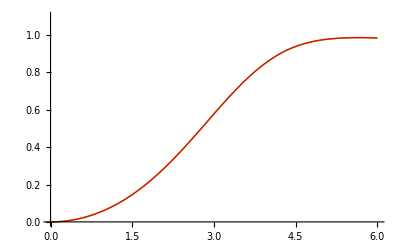

```mathematica
kinePlot=Plot[kineEnergy,{T,0,simDuration},DisplayFunction->Identity,PlotStyle->RGBColor[1, 0,0]];
kinePlotMat=Plot[kineEnergyMat,{T,0,simDuration},DisplayFunction->Identity,PlotStyle->RGBColor[0, 1,0]];
springPlot=Plot[springEnergy,{T,0,simDuration},DisplayFunction->Identity,PlotStyle->{RGBColor[0, 0,1]}];
totPlot=Plot[totEnergy,{T,0,simDuration},DisplayFunction->Identity,PlotStyle->{RGBColor[0, 0,0]}];

Show[kinePlotMat,kinePlot,DisplayFunction->$DisplayFunction,PlotRange->{{0,simDuration},{0,1.1}}]
```

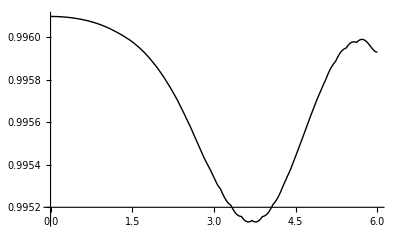

```mathematica
Show[totPlot,DisplayFunction->$DisplayFunction]
```

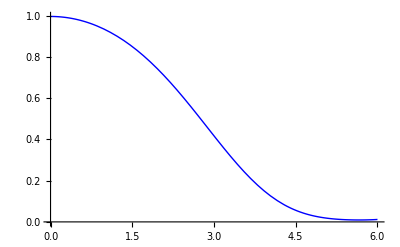

```mathematica
Show[springPlot,DisplayFunction->$DisplayFunction]
```

```mathematica
kinePlot=Plot[kineEnergy[All]/.sol,{T,0,simDuration},DisplayFunction->Identity,PlotStyle->RGBColor[1, 0,0]];
springPlot=Plot[springEnergy[T]/.sol,{T,0,simDuration},DisplayFunction->Identity,PlotStyle->{RGBColor[0, 0,1],Dashed}];
totPlot=Plot[(kineEnergy[T]+springEnergy[T])/.sol,{T,0,simDuration},DisplayFunction->Identity,PlotStyle->{RGBColor[0, 0,0]}];
Show[springPlot,kinePlot,totPlot,DisplayFunction->$DisplayFunction]
```

-Graphics-

### Export data

```mathematica
(* P1 on carpus *)
carp1Kine=
{((Location[Point[carpus,1]]/.sol/.{T->tEval})/sL)[[1]],((Location[Point[carpus,1]]/.sol/.{T->tEval})/sL)[[2]],
((Velocity[Point[carpus,1]]/.sol/.{T->tEval})/sL * sT)[[1]],((Velocity[Point[carpus,1]]/.sol/.{T->tEval})/sL * sT)[[2]],
((Acceleration[Point[carpus,1]]/.sol/.{T->tEval})/sL * sT^2)[[1]],((Acceleration[Point[carpus,1]]/.sol/.{T->tEval})/sL * sT^2)[[2]]
};
Export[StringJoin[currPath, "/carpusP1.mat"],carp1Kine,"MAT"];
```

Export::nodir: Directory "/Volumes/Docs/Projects/Patek_project/sims/" does not exist.

```mathematica
(* P2 on carpus *)
carp2Kine=
{((Location[Point[carpus,2]]/.sol/.{T->tEval})/sL)[[1]],((Location[Point[carpus,2]]/.sol/.{T->tEval})/sL)[[2]],
((Velocity[Point[carpus,2]]/.sol/.{T->tEval})/sL * sT)[[1]],((Velocity[Point[carpus,2]]/.sol/.{T->tEval})/sL * sT)[[2]],
((Acceleration[Point[carpus,2]]/.sol/.{T->tEval})/sL * sT^2)[[1]],((Acceleration[Point[carpus,2]]/.sol/.{T->tEval})/sL * sT^2)[[2]]
};
Export[StringJoin[currPath, "/carpusP2.mat"],carp2Kine,"MAT"];
```

Export::nodir: Directory "/Volumes/Docs/Projects/Patek_project/sims/" does not exist.

```mathematica
(* P1 on ground *)
gnd1Kine=
{((Location[Point[ground,1]]/.sol/.{T->tEval})/sL)[[1]],((Location[Point[ground,1]]/.sol/.{T->tEval})/sL)[[2]],
((Velocity[Point[ground,1]]/.sol/.{T->tEval})/sL * sT)[[1]],((Velocity[Point[ground,1]]/.sol/.{T->tEval})/sL * sT)[[2]],
((Acceleration[Point[ground,1]]/.sol/.{T->tEval})/sL * sT^2)[[1]],((Acceleration[Point[ground,1]]/.sol/.{T->tEval})/sL * sT^2)[[2]]
};
Export[StringJoin[currPath, "/groundP1.mat"],gnd1Kine,"MAT"];
```

Export::nodir: Directory "/Volumes/Docs/Projects/Patek_project/sims/" does not exist.

```mathematica
(* P1 on mV *)
mV1Kine=
{((Location[Point[mV,1]]/.sol/.{T->tEval})/sL)[[1]],((Location[Point[mV,1]]/.sol/.{T->tEval})/sL)[[2]],
((Velocity[Point[mV,1]]/.sol/.{T->tEval})/sL * sT)[[1]],((Velocity[Point[mV,1]]/.sol/.{T->tEval})/sL * sT)[[2]],
((Acceleration[Point[mV,1]]/.sol/.{T->tEval})/sL * sT^2)[[1]],((Acceleration[Point[mV,1]]/.sol/.{T->tEval})/sL * sT^2)[[2]]
};
Export[StringJoin[currPath, "/mVP1.mat"],mV1Kine,"MAT"];
```

Export::nodir: Directory "/Volumes/Docs/Projects/Patek_project/sims/" does not exist.

```mathematica
(* P1 on dactyl *)
dac1Kine=
{((Location[Point[dactyl,1]]/.sol/.{T->tEval})/sL)[[1]],((Location[Point[dactyl,1]]/.sol/.{T->tEval})/sL)[[2]],
((Velocity[Point[dactyl,1]]/.sol/.{T->tEval})/sL * sT)[[1]],((Velocity[Point[dactyl,1]]/.sol/.{T->tEval})/sL * sT)[[2]],
((Acceleration[Point[dactyl,1]]/.sol/.{T->tEval})/sL * sT^2)[[1]],((Acceleration[Point[dactyl,1]]/.sol/.{T->tEval})/sL * sT^2)[[2]]
};
Export[StringJoin[currPath, "/dactylP1.mat"],dac1Kine,"MAT"];
```

Mech::nopoint: Point number 1 on body number 4 is not present in the
current system.

General::stop: Further output of Mech :: "nopoint" will be suppressed during this calculation.

Export::nodir: Directory "/Volumes/Docs/Projects/Patek_project/sims/" does not exist.

```mathematica
(* Moment from spring *)
springM = (springMoment
/.sol/.{T->tEval})/sM/sL^2*sT^2;
Export[StringJoin[currPath, "/springMoment.mat"],springM,"MAT"];
```

Export::nodir: Directory "/Volumes/Docs/Projects/Patek_project/sims/" does not exist.

```mathematica
(* Moment from drag *)
dragM = (dragMoment
/.sol/.{T->tEval}) /sM/sL^2*sT^2;
Export[StringJoin[currPath, "/dragMoment.mat"],dragM,"MAT"];
```

Export::nodir: Directory "/Volumes/Docs/Projects/Patek_project/sims/" does not exist.

```mathematica
(* mV angle*)
Export[StringJoin[currPath, "/mvAng.mat"],Angle[mV,1]/.sol/.{T->tEval},"MAT"];
```

Export::nodir: Directory "/Volumes/Docs/Projects/Patek_project/sims/" does not exist.

```mathematica
(* dactyl angle*)
Export[StringJoin[currPath, "/dacAng.mat"],Angle[mV,1]/.sol/.{T->tEval},"MAT"];
```

Export::nodir: Directory "/Volumes/Docs/Projects/Patek_project/sims/" does not exist.